## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/andes/LogProcessing/self-improved-tutor

```mathematica
journalStyle={FontSize->9 (* ACM default font for text (10 for large journal format) *)};
figureWidth=72 If[False,6.5 (* Maximum allowed width for ACM journal large format. *),
	10/3 (* ACM journal column with for two-column format. *)];
```

```mathematica
data=Import["guerra-summer-2012-expectation.csv"];
```

```mathematica
Take[data,5]
```

{{Section,student,KC,condition,prob,gain,gainSquared,L,LSquared},{asu_7e256268bab914fb5asul1_,md5:3f6382444a54a0b87ee01b3eb66502db,draw-vector-aligned-axes,control,0.268941,0,0,0.268941,0.268941},{asu_7e256268bab914fb5asul1_,md5:3f6382444a54a0b87ee01b3eb66502db,draw-vector-aligned-axes,mlh,0,0,0,0,0},{asu_7e256268bab914fb5asul1_,md5:b5a232d14b85a64078d32c873932fe4c,draw-vector-aligned-axes,control,0.51825,0,0,1.81388,6.99638},{asu_7e256268bab914fb5asul1_,md5:b5a232d14b85a64078d32c873932fe4c,draw-vector-aligned-axes,mlh,0.129563,0,0,0.129563,0.129563}}

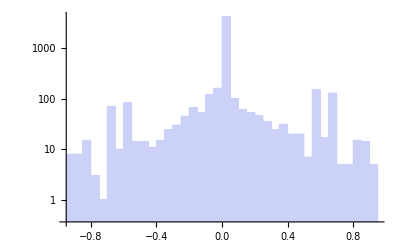

```mathematica
Histogram[Map[#[[6]]&,Rest[data]],ScalingFunctions->"Log"]
```

Need to group into KCs, remove header row.

```mathematica
Print[conditions=Union[Map[#[[4]]&,Rest[data]]]];
Length[allKCs=Union[Map[#[[3]]&,Rest[data]]]]
```

{control,mlh}

289

```mathematica
analyzeKC[subdata_]:=Block[{probs=Map[#[[5]]&,subdata],gains=Map[#[[6]]&,subdata],gains2=Map[#[[7]]&,subdata],step=Map[#[[8]]&,subdata],step2=Map[#[[9]]&,subdata]},
(* Make sure there is data for each condition and that the errors can be estimated. *)
If[0<Total[probs] (*&& Total[step2]*Total[probs]>Total[step]^2 &&  Total[gains2]*Total[probs]>Total[gains]^2*), 
(* learning step averaged over students and associated standard error. *)
{{Total[step]/Total[probs],Sqrt[Total[step2]-Total[step]^2/Total[probs]]/Total[probs]},
(* performance gain averaged over students along with associated standard error. *)
{Total[gains]/Total[probs],Sqrt[Total[gains2]-Total[gains]^2/Total[probs]]/Total[probs]}}]]
```

```mathematica
diffs=Outer[Function[{kc,condition},analyzeKC[Select[Rest[data],(#[[3]]==kc && #[[4]]==condition)&]]],allKCs,conditions]
```

{{{{2.57039,1.09592},{0.286444,0.238956}},Null},{{{1.14351,0.241471},{-0.282435,0.620863}},{{1.,0.},{0.688845,0.497977}}},{Null,Null},{{{1.09334,0.228508},{0.787387,0.298158}},{{1.,0.},{-0.333333,0.705443}}},{{{1.50361,0.381246},{0.518077,0.262712}},{{1.52999,0.324547},{0.246685,0.270433}}},{Null,Null},{{{14.4785,3.27911},{-0.0387444,0.146821}},{{16.7087,5.11358},{-0.0604793,0.114581}}},{{{2.35377,1.00675},{-0.249941,0.372232}},{{1.,0.},{0.,0.}}},{{{32.813,7.80883},{-0.15691,0.130669}},{{31.8665,7.77534},{-0.027923,0.0980557}}},{{{12.0164,2.81199},{-0.157729,0.116328}},{{13.8874,3.59293},{-0.0652318,0.126257}}},{{{4.08107,1.28353},{0.241777,0.202618}},{{3.87512,0.962539},{0.469363,0.203564}}},{{{1.,0.},{0.688845,0.497977}},Null},{{{1.08753,0.181608},{0.491756,0.32127}},{{1.08753,0.181608},{0.,0.450644}}},{Null,Null},{{{2.43314,1.28306},{0.380933,0.288675}},{{1.7096,0.427846},{0.275683,0.295243}}},{{{1.46105,0.875094},{0.115263,0.218773}},{{2.20179,0.787018},{0.0151186,0.0943426}}},{Null,Null},{{{1.,0.},{0.,0.}},{{1.5,0.767975},{0.,0.}}},{{{1.,6.49233×10^-9},{0.183429,0.521718}},{{1.,0.},{0.688845,0.287507}}},{{{1.30591,0.553596},{0.,0.}},{{1.,0.},{1.,0.}}},{{{9.34655,2.34232},{-0.11462,0.148749}},{{9.68239,2.57411},{-0.028044,0.169478}}},{Null,Null},{{{1.,0.},{-0.424607,0.295157}},{{1.,0.},{0.,0.48145}}},{{{6.59724,1.57753},{0.0596507,0.104636}},{{6.62873,1.51339},{0.101876,0.222035}}},{{{3.09223,0.980352},{-0.246557,0.184349}},{{3.30982,0.896162},{-0.246407,0.190993}}},{{{1.89863,0.52175},{-0.0183189,0.0501975}},{{2.29655,0.567516},{-0.00851968,0.160634}}},{{{3.18002,2.59624},{-0.618002,0.259624}},{{1.89273,1.07519},{-0.835535,0.215731}}},{{{2.05309,0.437519},{-0.271769,0.277522}},{{1.84835,0.500024},{0.656954,0.273038}}},{{{1.69349,0.737778},{0.,0.220559}},{{1.,0.+1.30595×10^-8 ⅈ},{0.,0.}}},{{{1.,0.},{0.898532,0.185467}},{{1.,0.+1.30595×10^-8 ⅈ},{0.,0.}}},{{{2.55377,0.90499},{0.,0.}},{{2.,0.460205},{0.,0.}}},{{{6.61666,1.96566},{0.0758351,0.190525}},{{7.40217,2.02745},{-0.0601841,0.171127}}},{{{1.09808,0.176995},{0.404589,0.340115}},{{1.43983,0.433465},{0.612038,0.288086}}},{Null,Null},{{{2.5334,0.714943},{-0.191037,0.195196}},{{2.14642,0.444538},{-0.201861,0.204717}}},{{{2.49147,1.08154},{0.201035,0.252334}},{{1.07713,0.160943},{0.650004,0.287731}}},{{{1.5,0.767975},{0.,0.}},Null},{{{1.9388,0.519486},{-0.0501325,0.109296}},{{2.0876,0.449117},{-0.207928,0.209975}}},{{{17.697,3.35426},{-0.0340668,0.103375}},{{16.4525,4.31078},{0.00117105,0.0967232}}},{{{2.59061,0.905582},{0.218785,0.236253}},{{2.90119,0.604357},{0.0649794,0.175959}}},{{{2.2195,0.557833},{-0.0722143,0.146364}},{{1.93059,0.471768},{-0.144788,0.275837}}},{Null,Null},{{{2.80245,0.815562},{-0.394214,0.224574}},{{1.86226,0.432362},{-0.0487611,0.106408}}},{{{2.52434,0.386486},{-0.482884,0.231109}},{{2.28931,0.466415},{-0.401889,0.28175}}},{{{4.25974,1.21001},{0.32017,0.194004}},{{3.32409,0.722582},{0.514431,0.21067}}},{{{1.65205,0.322954},{0.634682,0.247191}},{{1.41212,0.306329},{0.263646,0.300486}}},{Null,Null},{{{6.76047,1.80389},{-0.36934,0.169231}},{{6.50687,1.69298},{-0.227342,0.256298}}},{{{2.05353,0.491811},{0.139858,0.320621}},{{2.15006,0.381651},{0.483659,0.277181}}},{{{1.77201,0.494751},{0.265158,0.229233}},{{1.81642,0.473963},{0.446865,0.267275}}},{{{1.,7.45951×10^-9},{0.,0.546269}},{{1.,0.},{-0.525372,0.331687}}},{{{2.16764,0.969736},{-0.339421,0.222498}},{{2.6666,0.932928},{-0.28483,0.238126}}},{{{1.49058,0.287468},{0.,0.}},{{1.44444,0.359785},{0.,0.}}},{{{1.,0.},{0.256186,0.549961}},{{1.2553,0.283234},{-0.287218,0.282222}}},{{{1.,0.},{1.,0.}},{{1.,0.},{0.,0.}}},{{{1.,0.},{1.,0.}},Null},{{{1.,0.+7.36334×10^-9 ⅈ},{0.624113,0.286306}},{{1.,0.},{0.596104,0.347169}}},{Null,Null},{{{7.26682,1.65001},{0.0110335,0.254533}},{{5.41665,1.74907},{0.418751,0.266575}}},{{{1.2,0.459942},{0.9,0.229971}},Null},{{{5.24131,1.80211},{0.246412,0.189129}},{{5.96413,1.73008},{0.145029,0.166282}}},{Null,{{1.,0.},{1.,0.}}},{{{2.85297,0.62843},{0.522853,0.192853}},{{1.83979,0.826081},{0.485318,0.260989}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.525372,0.469076}}},{{{1.82602,0.4304},{-0.147,0.305053}},{{1.68711,0.396474},{0.48163,0.266334}}},{{{373.153,94.8515},{-0.0447918,0.0523573}},{{354.386,115.357},{0.0568573,0.05803}}},{Null,Null},{{{1.91396,0.371549},{0.355111,0.248796}},{{2.38941,0.518393},{-0.287391,0.236713}}},{Null,Null},{Null,{{1.,0.},{1.,0.}}},{{{1.37455,0.547716},{0.534798,0.315233}},{{1.,0.},{1.,0.}}},{{{5.79692,1.27999},{-0.241919,0.191881}},{{5.41855,1.16052},{-0.111253,0.20915}}},{Null,Null},{Null,Null},{Null,Null},{{{1.12133,0.216117},{0.521688,0.368644}},{{1.,0.},{0.469646,0.313428}}},{Null,Null},{Null,Null},{{{1.31084,0.270804},{0.1942,0.386987}},{{1.5,0.268483},{0.,0.360441}}},{{{1.,0.},{0.,0.}},Null},{{{3.83894,0.919532},{0.0112064,0.215887}},{{4.91627,1.14035},{0.327376,0.166662}}},{{{5.55878,1.07258},{-0.200913,0.198553}},{{4.71831,1.55652},{0.0329048,0.25321}}},{Null,Null},{Null,Null},{{{2.19885,0.492357},{0.232509,0.210685}},{{2.37243,0.684447},{0.247966,0.223493}}},{{{3.32192,0.819702},{0.180005,0.233945}},{{2.93417,0.623209},{0.232558,0.201336}}},{Null,{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},{{1.,0.},{-1.,0.}}},{{{30.2757,7.23182},{-0.181292,0.135041}},{{37.4838,8.987},{-0.25225,0.152607}}},{{{1.,0.},{0.,0.}},Null},{{{1.68551,0.430672},{0.251951,0.30958}},{{2.22393,0.580411},{-0.204571,0.248803}}},{{{10.2275,2.01627},{-0.278914,0.121364}},{{13.6193,3.27375},{-0.412377,0.181727}}},{{{2.,0.508456},{0.92381,0.148861}},Null},{{{1.87877,0.57537},{-0.323197,0.347512}},{{1.67394,0.349772},{-0.242016,0.308949}}},{{{2.87931,0.52279},{-0.0769098,0.23394}},{{2.93244,0.697443},{-0.32073,0.160098}}},{{{1.,0.},{0.,0.}},Null},{{{3.21531,0.973819},{0.0892245,0.232899}},{{2.64755,0.902585},{0.255454,0.188359}}},{{{1.39214,0.437259},{0.,0.29848}},Null},{Null,Null},{Null,Null},{Null,Null},{Null,Null},{{{1.14141,0.227285},{-0.169326,0.511927}},{{1.05927,0.147806},{-0.436939,0.547357}}},{{{1.,0.},{0.,0.}},Null},{{{1.99024,0.765166},{0.,0.}},{{1.72605,0.464285},{0.,0.}}},{{{3.17784,0.681741},{-0.26964,0.247574}},{{3.43605,0.664132},{-0.258551,0.221368}}},{Null,Null},{{{1.18064,0.233854},{0.,0.425997}},{{1.23807,0.297207},{0.,0.181209}}},{Null,Null},{Null,Null},{{{1.73788,0.406821},{-0.465645,0.306861}},{{1.37383,0.366409},{0.125753,0.31082}}},{{{3.24529,1.07205},{0.431712,0.200758}},{{2.86142,0.682809},{0.359406,0.230259}}},{{{1.72643,0.483945},{0.578192,0.235546}},{{1.68027,0.407976},{0.495964,0.266709}}},{{{1.78586,0.848314},{0.309334,0.289353}},{{1.18178,0.25549},{0.694669,0.268056}}},{{{4.25405,1.24622},{0.0670369,0.189272}},{{3.9538,1.00539},{0.0570634,0.116163}}},{Null,Null},{{{3.14954,1.23668},{0.306861,0.300196}},{{1.5,0.292888},{0.,0.4095}}},{{{1.,0.},{1.,0.}},Null},{{{1.,0.},{0.,0.}},Null},{{{1.45707,0.449275},{-0.172429,0.308096}},{{1.90151,0.62318},{0.146077,0.27378}}},{{{1.59015,0.485706},{-0.66392,0.426209}},{{1.20455,0.302717},{0.0480458,0.625664}}},{Null,Null},{Null,Null},{Null,Null},{Null,Null},{{{1.43609,0.551599},{0.439188,0.37838}},Null},{{{5.13855,1.35919},{-0.200882,0.188788}},{{3.18461,0.697986},{-0.360219,0.239193}}},{Null,Null},{{{2.36136,1.00465},{0.899226,0.194596}},Null},{{{1.87961,0.738643},{0.141989,0.502722}},{{1.,0.},{0.768558,0.276653}}},{{{1.36657,0.490826},{0.248912,0.432627}},{{2.21779,1.04762},{0.743921,0.296005}}},{{{1.53653,0.288397},{-0.177083,0.247858}},{{1.3685,0.284465},{0.184103,0.25681}}},{{{2.1323,0.714181},{0.0347918,0.229161}},{{2.5029,1.30639},{0.02122,0.0570064}}},{{{4.91724,1.23182},{0.0121235,0.212026}},{{5.82484,1.6193},{0.078602,0.247347}}},{{{2.39936,0.722439},{-0.0683674,0.285354}},{{2.45562,0.672427},{0.185219,0.269901}}},{Null,Null},{Null,Null},{{{1.18839,0.260685},{0.26462,0.294088}},{{1.17221,0.34034},{0.,0.}}},{{{6.55156,1.4991},{-0.0448436,0.183468}},{{8.9908,2.17998},{-0.0827563,0.181803}}},{{{3.26244,0.887528},{0.352481,0.201927}},{{3.07628,0.779143},{0.143,0.242063}}},{{{1.,0.},{0.,0.}},{{1.,0.},{0.,0.}}},{{{10.5312,2.47554},{-0.233031,0.144303}},{{12.7801,2.31444},{-0.350162,0.143975}}},{{{4.79195,1.10682},{-0.0372726,0.127555}},{{5.17165,1.29889},{0.0784143,0.0701378}}},{{{2.41668,0.554051},{0.471073,0.245465}},{{2.57429,0.770032},{-0.144145,0.205573}}},{{{4.42808,1.04032},{-0.433538,0.159561}},{{5.56165,0.932425},{-0.32443,0.17968}}},{{{1.38708,0.389584},{0.435465,0.376552}},{{1.17221,0.34034},{0.,0.}}},{{{3.80924,0.912336},{0.0707111,0.197166}},{{3.28953,0.947573},{0.267216,0.252818}}},{{{13.373,3.01845},{0.150534,0.109055}},{{15.2965,3.36429},{-0.118626,0.165514}}},{{{1.37772,0.592045},{-0.428658,0.419912}},Null},{{{8.47799,2.25046},{-0.0111782,0.180055}},{{8.76707,2.43128},{0.0793994,0.205028}}},{{{1.,0.},{1.,0.}},{{1.,0.},{0.,0.}}},{{{1.39602,0.335858},{0.295102,0.474071}},{{1.,0.},{0.,0.}}},{{{1.13077,0.16998},{0.648724,0.230298}},{{1.20337,0.339639},{0.692383,0.287336}}},{{{250.785,79.663},{0.0851122,0.0454388}},{{318.436,92.8311},{0.0759271,0.0240646}}},{{{1.,0.},{0.,0.}},Null},{Null,Null},{{{2.45279,0.483924},{-0.148127,0.264436}},{{1.91754,0.541949},{0.312489,0.303011}}},{{{2.86328,0.885686},{-0.300241,0.308406}},{{1.98447,0.484724},{0.0414123,0.30385}}},{Null,Null},{{{1.5,0.505651},{0.,0.380578}},{{1.5,0.671829},{0.,0.671829}}},{Null,Null},{{{1.2,0.459942},{-0.9,0.229971}},Null},{{{2.28361,0.463622},{-0.409124,0.226175}},{{2.,0.442207},{0.,0.301132}}},{Null,Null},{{{1.,0.},{0.,0.}},Null},{{{1.49653,0.47614},{0.,0.}},{{1.57236,0.279385},{0.217077,0.28021}}},{{{1.,0.},{0.688845,0.497977}},{{1.,0.},{0.,0.}}},{{{1.,0.},{0.688845,0.497977}},{{1.,0.},{0.,0.}}},{{{1.,0.},{0.,0.}},{{1.,0.},{1.,0.}}},{{{151.471,44.1333},{0.0329174,0.101173}},{{187.684,47.9703},{0.0330328,0.074792}}},{Null,Null},{{{1.,0.},{0.407879,0.471632}},{{1.,0.},{0.,0.631256}}},{Null,{{1.,0.},{0.,0.}}},{{{1.62951,0.368804},{0.354473,0.377749}},{{1.53453,0.343208},{0.462869,0.257846}}},{{{1.32614,0.484816},{0.465678,0.301353}},{{1.,0.},{1.,0.}}},{{{1.,0.},{0.,0.}},Null},{{{1.73833,0.404821},{-0.00363929,0.366417}},{{1.63108,0.472174},{0.0991189,0.340166}}},{Null,Null},{{{1.,0.+6.60943×10^-9 ⅈ},{-0.746949,0.24348}},{{1.,0.},{0.256186,0.549961}}},{{{1.,0.+6.60943×10^-9 ⅈ},{0.746949,0.24348}},{{1.,0.},{0.424607,0.417416}}},{Null,{{1.,0.},{1.,0.}}},{{{1.,0.},{1.,0.}},{{1.,0.},{0.,0.}}},{{{2.26846,0.499943},{-0.0905419,0.293101}},{{2.22891,0.813936},{-0.573619,0.233358}}},{{{1.24271,0.35046},{0.448401,0.385218}},{{1.29137,0.271355},{-0.0269729,0.398068}}},{Null,Null},{{{1.39214,0.437259},{0.,0.29848}},Null},{Null,Null},{{{1.5,0.671829},{0.,0.671829}},Null},{Null,Null},{Null,Null},{{{3.5323,0.93759},{0.156787,0.24418}},{{3.72012,0.763576},{0.0933729,0.233931}}},{{{1.,0.},{-0.424607,0.417416}},{{1.05004,0.125402},{0.619105,0.271793}}},{{{1.54874,0.434717},{-0.239903,0.234535}},{{1.59488,0.609497},{0.,0.276162}}},{{{1.27228,0.443887},{0.308997,0.332884}},{{2.0207,0.549334},{-0.0798376,0.389499}}},{{{2.,1.1031},{0.550538,0.30693}},{{1.,0.},{0.815758,0.320878}}},{{{1.89708,0.340138},{-0.160403,0.312818}},{{1.31492,0.330926},{0.224978,0.445758}}},{{{1.97639,0.807103},{-0.509627,0.390439}},{{1.,0.},{0.,0.747559}}},{{{2.93187,0.841011},{-0.196347,0.250445}},{{2.40168,0.671826},{0.167721,0.361317}}},{{{1.19599,0.251335},{-0.477364,0.34967}},{{1.,0.},{-0.553196,0.479222}}},{{{1.44073,0.715942},{0.,0.}},{{1.,0.+2.48576×10^-8 ⅈ},{0.,0.}}},{Null,Null},{{{1.20353,0.345155},{0.,0.273473}},{{1.19643,0.226365},{-0.0276947,0.50571}}},{Null,Null},{Null,Null},{{{1.,1.02541×10^-8},{0.289712,0.61812}},{{1.,0.},{-0.688845,0.352123}}},{{{2.22339,0.547282},{0.868587,0.185527}},{{1.,0.},{0.,0.}}},{{{3.07227,1.09433},{0.0830826,0.274964}},{{2.54977,0.735652},{-0.0172809,0.404266}}},{{{2.,1.1031},{0.550538,0.30693}},Null},{{{1.76807,0.471002},{0.633578,0.2239}},{{2.08882,0.422926},{0.389896,0.288844}}},{{{1.46133,0.267335},{0.,0.326106}},{{1.53342,0.267644},{0.337959,0.36729}}},{{{2.21737,0.493281},{0.131398,0.311692}},{{2.05372,0.922817},{-0.0063825,0.395656}}},{{{1.,0.},{0.,0.}},Null},{Null,Null},{{{1.,0.},{1.,0.}},Null},{{{1.30729,0.311468},{0.492062,0.347605}},{{1.83008,0.430784},{0.406334,0.318108}}},{{{2.15448,0.776947},{-0.0289128,0.330318}},{{2.07462,0.533004},{0.217866,0.248306}}},{{{4.32097,0.914332},{0.156907,0.215774}},{{3.43542,0.895197},{0.490453,0.188098}}},{{{2.82306,1.02597},{0.0149436,0.330529}},{{3.24675,0.922435},{0.267634,0.203105}}},{{{1.11606,0.237025},{0.326045,0.34689}},{{1.28087,0.263507},{0.234008,0.444837}}},{Null,Null},{Null,Null},{Null,Null},{{{1.,0.},{0.,0.}},Null},{Null,Null},{Null,Null},{Null,Null},{{{1.,0.},{0.,0.}},{{1.,0.},{-0.688845,0.497977}}},{{{4.90289,1.15383},{0.158524,0.202164}},{{3.54733,0.812297},{0.560576,0.136295}}},{{{110.627,28.2137},{0.0346613,0.066773}},{{130.897,34.0056},{0.0372612,0.0729427}}},{Null,Null},{{{3.34705,1.04792},{-0.213724,0.258897}},{{2.82135,0.869146},{-0.390315,0.264858}}},{{{1.35915,0.411199},{-0.437394,0.505481}},{{1.,0.},{0.442599,0.428246}}},{{{1.50153,0.458741},{-0.280213,0.34579}},{{2.05042,0.412019},{-0.470258,0.262681}}},{{{3.9237,1.37002},{0.196168,0.227721}},{{3.27011,0.864564},{-0.0152188,0.24682}}},{{{2.75565,0.696247},{0.0669372,0.192402}},{{2.12862,0.682199},{0.456904,0.221652}}},{{{1.53475,0.540403},{0.376229,0.384614}},{{1.14351,0.241471},{0.282435,0.620863}}},{Null,{{1.,0.},{0.,0.}}},{{{3.50185,1.07419},{-0.0775046,0.262811}},{{3.63045,0.883579},{-0.125725,0.145668}}},{{{1.44637,0.470359},{0.229074,0.401071}},{{1.,0.},{0.356275,0.370454}}},{{{2.89541,0.85202},{0.0530609,0.235645}},{{4.09908,1.36303},{-0.0611123,0.253416}}},{{{1.5,0.767975},{0.,0.}},Null},{{{4.73071,1.04397},{-0.223628,0.172053}},{{4.45765,0.938189},{-0.103016,0.218325}}},{Null,Null},{{{6.9504,1.95204},{0.228577,0.202082}},{{7.16602,1.73573},{0.137732,0.204266}}},{{{1.,0.},{0.,0.}},{{1.52659,0.438406},{-0.594831,0.322684}}},{Null,Null},{Null,Null},{{{3.,0.627226},{-0.937204,0.124471}},{{1.78825,0.715609},{0.762862,0.295039}}},{{{1.,0.},{0.,0.}},{{1.,0.},{-1.,0.}}},{{{4.70981,1.08247},{0.226088,0.172235}},{{6.4861,1.60572},{-0.270609,0.20928}}},{Null,Null},{{{3.30403,0.831497},{0.694008,0.194948}},{{1.71263,0.43456},{0.438821,0.279436}}},{{{1.,0.},{0.,0.}},Null},{Null,Null},{Null,Null},{{{1.,0.},{0.525372,0.331687}},{{1.,0.},{0.356275,0.370454}}},{{{1.,7.45951×10^-9},{0.,0.546269}},{{1.10854,0.194739},{0.,0.451866}}},{Null,Null},{{{1.,0.},{-1.,0.}},{{1.,0.},{0.,0.}}},{Null,Null},{{{1.,0.},{0.,0.}},Null},{{{2.42501,0.906267},{0.356269,0.231149}},{{2.89417,0.984313},{-0.227868,0.273524}}},{{{1.5,0.671829},{0.,0.671829}},{{1.,0.},{0.,0.}}},{{{1.91536,0.468048},{0.0703619,0.185639}},{{2.07641,0.379619},{-0.0702061,0.319534}}},{{{1.5,0.767975},{0.,0.}},Null},{{{3.30219,1.30779},{0.386175,0.216879}},{{4.29073,1.66219},{0.375409,0.183195}}},{{{1.37666,0.258862},{-0.169928,0.292191}},{{1.63344,0.353971},{0.094906,0.329955}}},{{{1.06894,0.14449},{0.774646,0.23829}},{{1.,7.45951×10^-9},{0.596104,0.347169}}},{{{1.19131,0.226854},{0.42447,0.277626}},{{1.,0.},{0.356275,0.370454}}},{{{1.,0.},{0.688845,0.497977}},Null},{{{1.12678,0.257347},{0.712333,0.350116}},{{1.,0.+2.48576×10^-8 ⅈ},{0.,0.}}},{{{1.45886,0.329249},{0.0579445,0.331869}},{{1.83414,0.426031},{0.509931,0.282078}}},{{{3.61472,1.07614},{-0.139132,0.274382}},{{2.65796,0.929016},{-0.129471,0.409837}}},{{{2.83858,0.708106},{0.117506,0.268027}},{{2.92792,0.793334},{0.377214,0.214557}}},{Null,Null},{Null,Null},{Null,Null},{Null,Null},{{{1.,0.},{0.,0.}},Null},{Null,Null},{Null,Null},{{{2.33825,0.791383},{0.45914,0.177488}},{{2.07326,0.672414},{0.435463,0.287944}}},{{{1.51991,0.481492},{0.525539,0.349929}},{{1.32511,0.313444},{-0.421304,0.250926}}},{{{1.,0.},{0.688845,0.497977}},Null},{Null,{{1.,0.},{1.,0.}}},{{{2.46151,0.584665},{0.63336,0.208243}},{{1.90506,0.417828},{-0.200747,0.331519}}},{Null,{{1.,0.},{0.,0.}}},{{{8.1602,2.18189},{0.113606,0.18927}},{{9.3753,2.49204},{-0.0368198,0.169354}}},{Null,Null}}

Scatter plot showing number of steps before mastery for each KC in each experimetal condition.

179

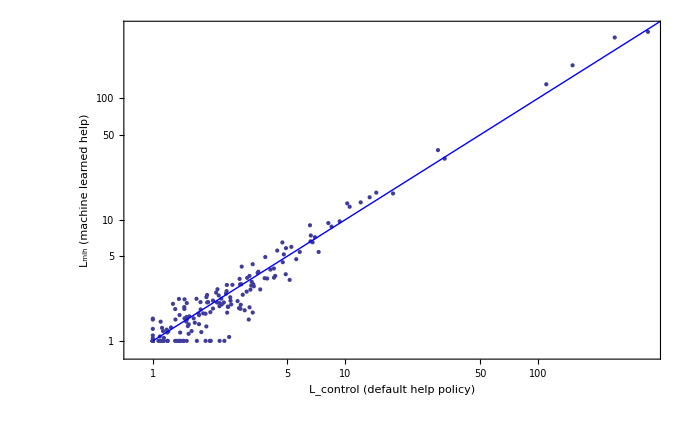

```mathematica
scatterStep=Block[{data=Map[{#[[1,1,1]],#[[2,1,1]]}&,Select[diffs,#[[1]]=!=Null && #[[2]]=!=Null&]]},Print[Length[data]];ListLogLogPlot[data,
(* Seems to be a bug in PlotRange->All, so do this by hand. *) 
PlotRange->{#,#}&[{0.8,Max[Flatten[data]]+10}],Epilog->{Blue,Line[{{0,0},{10,10}}]},Axes->False,Frame->True,FrameLabel->{"L_control (default help policy)","L_mlh (machine learned help)"},BaseStyle->If[True (* Choose between paper and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]]
```

```mathematica
.
```

For Presentation, want width 8.5 in = 612 pt and presentation BaseStyle.  Just doing clipboard cut and paste has trouble with some characters.  Graphics using eps in OpenOffice do not render in pdf output.

```mathematica
Export["scatter-step.png",scatterStep,ImageSize->612]
```

scatter-step.png

```mathematica
Export["scatter-step.eps",scatterStep,ImageSize->figureWidth]
```

scatter-step.eps

Data points where estimated error is zero distort the sum.  Set a minimum error of 1 turn for each

```mathematica
xx=Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],(* regular mean *) {Mean[val],Sqrt[err.err]/Length[val],StandardDeviation[val]/Sqrt[Length[val]]},(* maximum likelihood maximizing weighed mean *){val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[2,1,1]]-#[[1,1,1]],Sqrt[Max[1,Abs[#[[1,1,2]]]]^2+Max[1,Abs[#[[2,1,2]]]]^2]}&,Select[diffs,#[[1]]=!=Null  && #[[2]]=!=Null&]]]]
```

{179,{0.583174,1.1755,0.459814},{-0.119711,0.114023}}

This is the  one-tailed p-value from a Z-test

```mathematica
Block[{z=xx[[3,1]]/xx[[3,2]]},(1+Erf[-Abs[z]/Sqrt[2]])/2]
```

0.146886

Select only cases where positive learning was seen in both conditions.  We see that there is almost no difference in the change in number of steps.

```mathematica
xx2=Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],(* regular mean *) {Mean[val],Sqrt[err.err]/Length[val]},(* maximum likelihood maximizing weighed mean *){val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[2,1,1]]-#[[1,1,1]],Sqrt[Max[1,Abs[#[[1,1,2]]]]^2+Max[1,Abs[#[[2,1,2]]]]^2]}&,Select[diffs,#[[1]]=!=Null && #[[2]]=!=Null && #[[2,1,1]]>1.5 && #[[1,1,1]]>1.5&]]]]
```

{99,{1.1572,2.12154},{-0.118003,0.1641}}

Scatter plot showing performance gain 1-s-g for each KC in each experimetal condition.

179

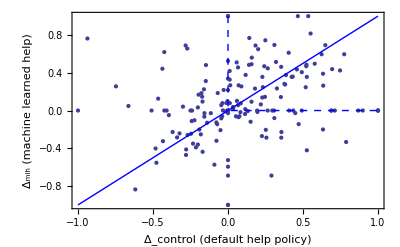

```mathematica
scatterGain=Block[{data=Map[{#[[1,2,1]],#[[2,2,1]]}&,Select[diffs,#[[1]]=!=Null && #[[2]]=!=Null&]]},Print[Length[data]];
ListPlot[data,
PlotRange->All,Epilog->{Blue,Line[{{-1,-1},{1,1}}],Dashed,Line[{{0,1},{0,0},{1,0}}]},Frame->True,Axes->False,FrameLabel->{"Δ_control (default help policy)","Δ_mlh (machine learned help)"},BaseStyle->If[True (* Choose between journal and presentation formatting *),journalStyle,{PointSize[.01],Thickness[0.005],FontSize->20}]]]
```

For Presentation, want width 6.4 in = 460 pt and presentation BaseStyle

```mathematica
Export["scatter-gain.png",scatterGain,ImageSize->460]
```

scatter-gain.png

```mathematica
Export["scatter-gain.eps",scatterGain,ImageSize->figureWidth]
```

scatter-gain.eps

```mathematica
yy=Block[{minErr=0.01},Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],(* regular mean *) {Mean[val],Sqrt[err.err]/Length[val],StandardDeviation[val]/Sqrt[Length[val]]},(* maximum likelihood maximizing weighed mean *){val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[2,2,1]]-#[[1,2,1]],Sqrt[Max[minErr,Abs[#[[1,2,2]]]]^2+Max[minErr,Abs[#[[2,2,2]]]]^2]}&,Select[diffs,#[[1]]=!=Null && #[[2]]=!=Null&]]]]]
```

{179,{-0.00147125,0.0299542,0.033199},{-0.138485,0.00372033}}

This is the  one-tailed p-value from a Z-test

```mathematica
Block[{z=yy[[3,1]]/yy[[3,2]]},(1+Erf[-Abs[z]/Sqrt[2]])/2]
```

0.0170913